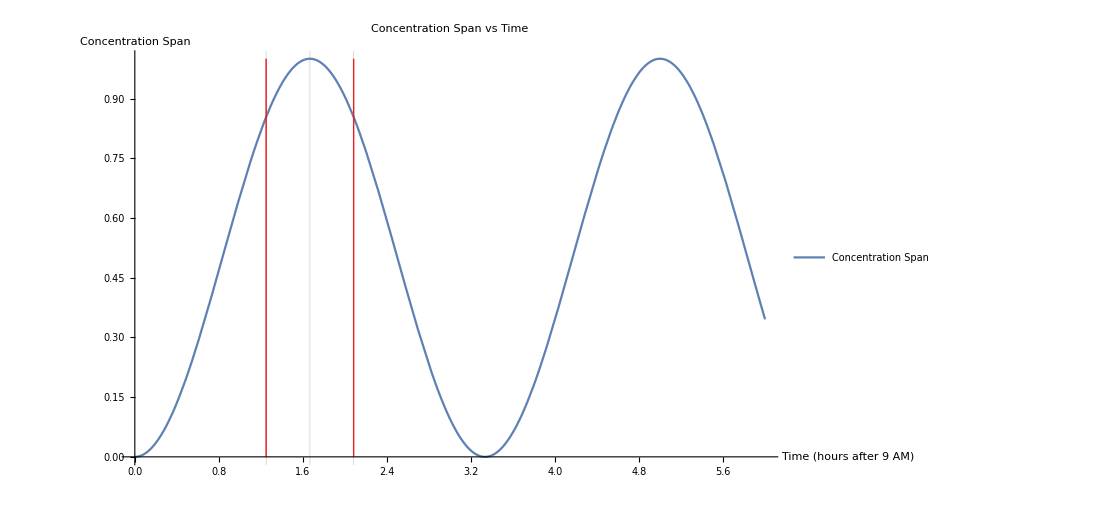

{0.853664,0.999989}

{1.,1.66667}

```mathematica
m[t_]:=1/2-1/2 Cos[(3 π/5) t]

maxResult=FindMaximum[{m[t],0<=t<=6},t];
maxConcentration=maxResult[[1]];
maxTime=t/. maxResult[[2]];

classDuration=0.833;
startTime=maxTime-classDuration/2;
endTime=maxTime+classDuration/2;

Plot[m[t],{t,0,6},PlotRange->{0,1},GridLines->{{maxTime,startTime,endTime},None},PlotLabel->"Concentration Span vs Time",AxesLabel->{"Time (hours after 9 AM)","Concentration Span"},Epilog->{Red,Line[{{startTime,0},{startTime,1}}],Line[{{endTime,0},{endTime,1}}]},PlotLegends->{"Concentration Span","Start of Class","End of Class"}]

(*Calculate the minimum and maximum concentration span during the class period*)
concentrationDuringClass=Table[m[t],{t,startTime,endTime,0.01}];
MinMax[concentrationDuringClass]

{maxConcentration,maxTime}
```